```mathematica
(* Enter File Path *)

SVDSet = Import["C:\\Users\\Robert\\Desktop\\Multi-mer Melts\\Octomer Melt\\Octomer_CD_Melt.txt", "Table"];
SetDirectory["C:\\Users\\Robert\\Desktop\\Multi-mer Melts\\Octomer Melt"];
```

```mathematica
(* Function Initiation and SVD *)

SingleStateMeltingFunction[T_,Sn_, Su_, dH_, Tm_]:= (Sn + Su*Exp[-((dH/R)*((1/Tm)-(1/T)))])/(1+Exp[-((dH/R)*((1/Tm)-(1/T)))]);
SingleStateFractionSn[T_, dH_, Tm_]:= 1/(1+Exp[-((dH/R)*((1/Tm)-(1/T)))]);
SingleStateFractionSu[T_, dH_, Tm_]:= (Exp[-((dH/R)*((1/Tm)-(1/T)))])/(1+Exp[-((dH/R)*((1/Tm)-(1/T)))]);

TwoStateMeltingFunction[T_,Sn_, S1_, Su_, dH1_, Tm1_, dH2_, Tm2_]:= (Sn + S1*Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Su*Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))])/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]);
TwoStateFractionSn[T_, dH1_, Tm1_, dH2_, Tm2_]:= 1/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]);
TwoStateFractionS1[T_, dH1_, Tm1_, dH2_, Tm2_]:= Exp[-((dH1/R)*((1/Tm1)-(1/T)))]/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]);
TwoStateFractionSu[T_, dH1_, Tm1_, dH2_, Tm2_]:= (Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))])/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]);


Clear[T,dH1,Tm1,dH2,Tm2, R];
K1[T_,dH1_, Tm1_] := Exp[(-dH1/R)*(1/Tm1-1/T)];
K2[T_, dH2_, Tm2_] := Exp[(-dH2/R)*(1/Tm2-1/T)];
K0[T_,dH1_, Tm1_, dH2_, Tm2_]:=K1[T,dH1,Tm1]/K2[T,dH2,Tm2];
Denom = 1+K0[T,dH1,Tm1,dH2,Tm2]+K0[T,dH1,Tm1,dH2,Tm2]*K2[T,dH2,Tm2];
ParallelFractionSn1[T_,dH1_,Tm1_,dH2_,Tm2_] := 1/Denom;
ParallelFractionSn2[T_,dH1_,Tm1_,dH2_,Tm2_] := K0[T,dH1,Tm1,dH2,Tm2]/Denom;
ParallelFractionSu[T_,dH1_,Tm1_,dH2_,Tm2_] := K1[T,dH1,Tm1]/Denom;
ParallelSpecies[T_, Sn1_, Sn2_, Su_, dH1_, Tm1_, dH2_, Tm2_]:= Sn1*ParallelFractionSn1[T, dH1, Tm1, dH2, Tm2]+Sn2*ParallelFractionSn2[T,dH1,Tm1,dH2,Tm2]+Su*ParallelFractionSu[T,dH1,Tm1,dH2,Tm2];

ThreeStateMeltingFunction[T_,Sn_, S1_, S2_, Su_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:= (Sn + S1*Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+S2*Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]+Su*Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]*Exp[-((dH3/R)*((1/Tm3)-(1/T)))])/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]*Exp[-((dH3/R)*((1/Tm3)-(1/T)))]);

ThreeStateFractionSn[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:= 1/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]*Exp[-((dH3/R)*((1/Tm3)-(1/T)))]);
ThreeStateFractionS1[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:= Exp[-((dH1/R)*((1/Tm1)-(1/T)))]/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]*Exp[-((dH3/R)*((1/Tm3)-(1/T)))]);
ThreeStateFractionS2[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:= (Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))])/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]*Exp[-((dH3/R)*((1/Tm3)-(1/T)))]);
ThreeStateFractionSu[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:= (Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]*Exp[-((dH3/R)*((1/Tm3)-(1/T)))])/(1+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]+Exp[-((dH1/R)*((1/Tm1)-(1/T)))]*Exp[-((dH2/R)*((1/Tm2)-(1/T)))]*Exp[-((dH3/R)*((1/Tm3)-(1/T)))]);

K1Int[T_, dH1_, Tm1_]:= Exp[-(dH1/R)*(1/Tm1-1/T)];
K2Int[T_,dH2_, Tm2_]:= Exp[-(dH2/R)*(1/Tm2-1/T)];
KUInt[T_, dH3_, Tm3_]:= Exp[-(dH3/R)*(1/Tm3-1/T)];
DenomInt= 1 + K1Int[T,dH1,Tm1]/K2Int[T,dH2,Tm2]+K1Int[T,dH1,Tm1]+K1Int[T,dH1,Tm1]*KUInt[T,dH3,Tm3];
ParallelIntFractionSn1[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_] := 1/DenomInt;
ParallelIntFractionSn2[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_] := (K1Int[T,dH1,Tm1]/K2Int[T,dH2,Tm2])/DenomInt;
ParallelIntFractionSI[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:= K1Int[T,dH1,Tm1]/DenomInt;
ParallelIntFractionSu[T_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:=KUInt[T,dH3,Tm3]*ParallelIntFractionSI[T, dH1, Tm1, dH2, Tm2, dH3, Tm3];
ParallelIntermediateFunction[T_, Sn1_, Sn2_, S1_, Su_, dH1_, Tm1_, dH2_, Tm2_, dH3_, Tm3_]:= Sn1*ParallelIntFractionSn1[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]+Sn2*ParallelIntFractionSn2[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]+S1*ParallelIntFractionSI[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]+Su*ParallelIntFractionSu[T, dH1, Tm1, dH2, Tm2, dH3, Tm3];

TraditionalForm[SingleStateMeltingFunction[T,Sn, Su, dH, Tm]];
TraditionalForm[TwoStateMeltingFunction[T,Sn, S1, Su, dH1, Tm1, dH2, Tm2]];
TraditionalForm[Simplify[ParallelSpecies[T, Sn1, Sn2, Su, dH1, Tm1, dH2, Tm2]]];
TraditionalForm[ThreeStateMeltingFunction[T, Sn, S1, S2, Su, dH1, Tm1, dH2, Tm2, dH3, Tm3]];
TraditionalForm[Simplify[ParallelIntermediateFunction[T,Sn1,Sn2,S1,Su,dH1,Tm1,dH2,Tm2,dH3,Tm2]]];

SingleTransitionModelAll={SingleStateMeltingFunction[T,Sn11,Su1,dH1,Tm1],SingleStateMeltingFunction[T,Sn12,Su2,dH1,Tm1], SingleStateMeltingFunction[T,Sn13,Su3,dH1,Tm1], SingleStateMeltingFunction[T,Sn14,Su4,dH1,Tm1]};
TwoTransitionModelAll={TwoStateMeltingFunction[T,Sn11,S11,Su1,dH1,Tm1,dH2,Tm2],TwoStateMeltingFunction[T,Sn12,S12,Su2,dH1,Tm1,dH2,Tm2],TwoStateMeltingFunction[T,Sn13,S13,Su3,dH1,Tm1,dH2,Tm2], TwoStateMeltingFunction[T,Sn14,S14,Su4,dH1,Tm1,dH2,Tm2]};
ParallelSpeciesModelAll={ParallelSpecies[T,Sn11,Sn21,Su1,dH1,Tm1,dH2,Tm2],ParallelSpecies[T,Sn12,Sn22,Su2,dH1,Tm1,dH2,Tm2],ParallelSpecies[T,Sn13,Sn23,Su3,dH1,Tm1,dH2,Tm2], ParallelSpecies[T,Sn14,Sn24,Su4,dH1,Tm1,dH2,Tm2]};
ThreeTransitionModelAll={ThreeStateMeltingFunction[T,Sn11,S11,S21,Su1,dH1,Tm1,dH2,Tm2,dH3,Tm3],ThreeStateMeltingFunction[T,Sn12,S12,S22,Su2,dH1,Tm1,dH2,Tm2,dH3,Tm3],ThreeStateMeltingFunction[T,Sn13,S13,S23,Su3,dH1,Tm1,dH2,Tm2,dH3,Tm3],ThreeStateMeltingFunction[T,Sn14,S14,S24,Su4,dH1,Tm1,dH2,Tm2,dH3,Tm3]};
ParallelIntModelAll={ParallelIntermediateFunction[T,Sn11,Sn21,S21,Su1,dH1,Tm1,dH2,Tm2,dH3,Tm3],ParallelIntermediateFunction[T,Sn12,Sn22,S22,Su2,dH1,Tm1,dH2,Tm2,dH3,Tm3],ParallelIntermediateFunction[T,Sn13,Sn23,S23,Su3,dH1,Tm1,dH2,Tm2,dH3,Tm3],ParallelIntermediateFunction[T,Sn14,Sn24,S24,Su4,dH1,Tm1,dH2,Tm2,dH3,Tm3]};

(* Data Import, SVD Export (Autocorrelations and Vectors) *)

Temperatures = SVDSet[[1]]+273.15;
Wavelengths = Table[SVDSet[[X,1]], {X, 2, Length[SVDSet]}];
Wavelengths;
Temp1 = Temperatures[[1]];
Temp2 = Temperatures[[Length[Temperatures]]];

Columns =Length[Temperatures];
Rows = Length[Wavelengths];
SVDMatrix = Table[{}, {X, 1, Rows}, {Y, 1, Columns}];
For[i = 1, i≤ Rows, i++,
{
For[j=1, j≤ Columns, j++,
{
SVDMatrix[[i,j]]=SVDSet[[i+1,j+1]]
}
]
}
];
MatrixForm[SVDMatrix];
{u,s,v}=SingularValueDecomposition[SVDMatrix];

Species = 10;

Newv = Table[Transpose[v][[x]], {x, 1, Species}];
Newv = Transpose[Newv];
MatrixForm[Newv];
ListPlot[Transpose[Newv][[3]]];

News = Table[0, {X, 1, Species}, {Y, 1, Species}];
For[m=1, m≤ Species, m++,
{
News[[m,m]]=s[[m,m]]
}
];
MatrixForm[News];

Newu = Table[Transpose[u][[x]], {x, 1, Species}];
Newu = Transpose[Newu];
MatrixForm[Newu];

MatrixForm[Newu.News.Transpose[Newv]];
VvectorFullSet = Table[{}, {i, 1, Species}];

Do[
VvectorFullSet[[i]] = Table[{Temperatures[[X]], News[[i,i]]*Transpose[Newv][[i,X]]}, {X, 1, Length[Temperatures]}]
, {i, 1, Species}];

VvectorFullSet[[1]] = Table[{Temperatures[[X]],News[[1,1]]*Transpose[Newv][[1,X]]}, {X, 1, Length[Temperatures]}];
VvectorFullSet[[2]] = Table[{Temperatures[[X]],News[[2,2]]*Transpose[Newv][[2,X]]}, {X, 1, Length[Temperatures]}];
VvectorFullSet[[3]] = Table[{Temperatures[[X]],News[[3,3]]*Transpose[Newv][[3,X]]}, {X, 1, Length[Temperatures]}];
VvectorFullSet[[4]] = Table[{Temperatures[[X]],News[[4,4]]*Transpose[Newv][[4,X]]}, {X, 1, Length[Temperatures]}];
VvectorFullSet[[5]] = Table[{Temperatures[[X]],News[[5,5]]*Transpose[Newv][[5,X]]}, {X, 1, Length[Temperatures]}];

P1 = ListPlot[VvectorFullSet[[1]]];
P2 = ListPlot[VvectorFullSet[[2]]];
P3 = ListPlot[VvectorFullSet[[3]]];
P4 = ListPlot[VvectorFullSet[[4]]];

ListPlot[VvectorFullSet, PlotRange-> All, PlotStyle-> PointSize[0.015]];
TableForm[VvectorFullSet];

ExportVs = Table[Transpose[Newv][[i,X]]*News[[i,i]], {X, 1, Length[Temperatures]}, {i, 1, Species}];
Do[PrependTo[ExportVs[[j]], Temperatures[[j]]-273.15], {j, 1, Length[Temperatures]}];

ExportUs = Table[-Transpose[Newu][[i,X]]*News[[i,i]], {X, 1, Length[Wavelengths]}, {i, 1, Species}];
Do[PrependTo[ExportUs[[j]], Wavelengths[[j]]], {j, 1, Length[Wavelengths]}];

SummedS = Sum[News[[i,i]], {i, 1, 10}];
CorrelationUandVTable = Table[{j, News[[j,j]],100*News[[j,j]]/SummedS, Sum[u[[i,j]]*u[[i+1,j]], {i, 1, Length[u]-1}],Sum[v[[i,j]]*v[[i+1,j]], {i, 1, Length[v]-1}]}, {j, 1, 10}];
PrependTo[CorrelationUandVTable, {"Species", "S-Value", "%S Value", "U-Autocorrelation", "V-Autocorrelation"}];
TableForm[%]

Export["V_Vectors.txt", ExportVs, "Table"];
Export["U_Vectors.txt", ExportUs, "Table"];
Export["Total_S_with_U_and_V_Autocorrelation_Table.txt", CorrelationUandVTable, "Table"];
```

Species | S-Value | %S Value | U-Autocorrelation | V-Autocorrelation
1 | 18102.4 | 64.5155 | 0.985778 | 0.981754
2 | 3228.42 | 11.5058 | 0.990183 | 0.972257
3 | 2172.45 | 7.74244 | 0.887698 | 0.283912
4 | 1168.35 | 4.16392 | 0.842804 | 0.0861694
5 | 1012.55 | 3.60867 | 0.971971 | 0.44032
6 | 736.814 | 2.62595 | 0.683635 | 0.0929337
7 | 510.316 | 1.81873 | 0.589475 | 0.0311103
8 | 460.749 | 1.64208 | 0.836108 | 0.217359
9 | 359.862 | 1.28252 | 0.787694 | 0.233012
10 | 307.081 | 1.09441 | 0.838911 | 0.153402

```mathematica
(*Differentiation of Vvectors for Tm Guesses*)

MaxValues = Table[{}, {i, 1, 5}];
MinValues = Table[{}, {i, 1, 5}];
AllValues = {};
For[j = 1, j≤ 5, j++,
{
Q1 = ListPlot[VvectorFullSet[[j]]];
Int1 = MovingAverage[VvectorFullSet[[j]], 3];
ListPlot[Int1];
IntDiffData = Interpolation[Int1];
Show[Q1, Plot[IntDiffData[Temp], {Temp, Int1[[1,1]], Int1[[Length[Int1],1]]}]]
D2 = D[IntDiffData[Temp],Temp];
Plot[D2, {Temp, Int1[[1,1]], Int1[[Length[Int1],1]]}];
T2 = Table[{Temp, D2}, {Temp, Int1[[1,1]], Int1[[Length[Int1],1]], 0.1}];
Smooth2 = MovingAverage[T2, 150];
ListPlot[Smooth2];
T1 = Table[Smooth2[[X,2]], {X, 1, Length[Smooth2]}];
For[i=1, i≤ Length[Smooth2], i++,
If[Smooth2[[i,2]]==Max[T1],
{
MaxValues[[j]] = Smooth2[[i,1]];
Break[];
}
];
];
For[i=1, i≤ Length[Smooth2], i++,
If[Smooth2[[i,2]]==Min[T1],
{
MinValues[[j]] = Smooth2[[i,1]];
Break[];
}
]
];
}
]
GuessHelp = Table[{i, MaxValues[[i]]-273.15,MinValues[[i]]-273.15}, {i, 1, 5}];
PrependTo[GuessHelp, {"Vvector", "PeakMaxTemp", "PeakMinTemp"}];
Do[AppendTo[AllValues, MaxValues[[x]]], {x, 1, 5}];
Do[AppendTo[AllValues, MinValues[[x]]], {x, 1, 5}];
TableForm[Sort[AllValues-273.15]]
Mean[AllValues]-273.15;
GuessHelpTm1 = Sort[AllValues][[1]]-273.15
GuessHelpTm2 = Mean[AllValues]-273.15
GuessHelpTm3 = Sort[AllValues][[10]]-273.15
TableForm[GuessHelp];
```

28.45
38.55
48.75
55.15
69.95
72.55
72.55
73.55
87.55
87.85

28.45

63.49

87.85

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

Best Guesses

Sn11Guess | Su1Guess
0 | 0
Sn12Guess | Su2Guess
0 | 0
Sn13Guess | Su3Guess
0 | 0
Sn14Guess | Su4Guess
0 | 0
dH1Guess | Tm1Guess
-30000 | 63.49

Single Transition Best Fit Results | 
Chi Squared | 1.40345×10^7
AIC Value | 2172.31
  | 
Sn11 | -3210.5
Su1 | -532.224
Sn12 | -77.7844
Su2 | 382.41
Sn13 | -3210.5
Su3 | -532.224
Sn14 | -77.7844
Su4 | 382.41
dH1 | -43.4692
Tm1 | 69.09
dG1 | -6.23512
  |

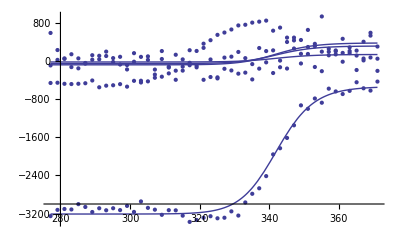

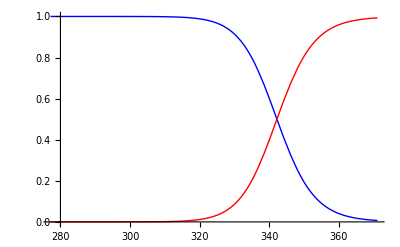

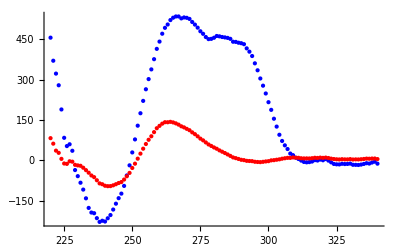

```mathematica
(* Single Transition Fitting *)

(* Single Transition Guesses *)

GuessTable = {};

Sn11Guess = 0;
Su1Guess =  0;

AppendTo[GuessTable, {"Sn11Guess", "Su1Guess"}];
AppendTo[GuessTable, {Sn11Guess, Su1Guess}];

Sn12Guess = 0;
Su2Guess =  0;

AppendTo[GuessTable, {"Sn12Guess", "Su2Guess"}];
AppendTo[GuessTable, {Sn12Guess, Su2Guess}]; 

Sn13Guess = 0;
Su3Guess =  0;

AppendTo[GuessTable, {"Sn13Guess", "Su3Guess"}];
AppendTo[GuessTable, {Sn13Guess, Su3Guess}];

Sn14Guess = 0;
Su4Guess =  0;

AppendTo[GuessTable, {"Sn14Guess", "Su4Guess"}];
AppendTo[GuessTable, {Sn14Guess, Su4Guess}]; 

dH1Guess = -30000;
Tm1Guess = GuessHelpTm2+273.15;

AppendTo[GuessTable, {"dH1Guess", "Tm1Guess"}];
AppendTo[GuessTable, {dH1Guess, Tm1Guess-273.15}];

R = 1.986;

(* Fitting Algorithm *)

Clear[i, Sn11, Su1, Sn12, Su2, dH1, Tm1];  (*  Clears any potential variables that will be minimized *)
LinkedChiSquared = Sum[((SingleTransitionModelAll[[i]]/.T->VvectorFullSet[[i,j,1]])-VvectorFullSet[[i,j,2]])^2, {j, Length[VvectorFullSet[[1]]]}, {i, 4}];
BestAnswerEver = FindMinimum[LinkedChiSquared, {{Sn11, Sn11Guess}, {Su1, Su1Guess},{Sn12, Sn12Guess}, {Su2, Su2Guess}, {Sn13, Sn13Guess}, {Su3, Su3Guess},{Sn14, Sn14Guess}, {Su4, Su4Guess},{dH1, dH1Guess}, {Tm1, Tm1Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000];

(* BestAnswerEver = FindMinimum[LinkedChiSquared, {{Sn11, Sn11Guess}, {Su1, Su1Guess},{Sn12, Sn12Guess}, {Su2, Su2Guess}, {dH1, dH1Guess}, {Tm1, Tm1Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000]; *)

SingleTransitionChiSquared = BestAnswerEver[[1]];
SingleTransitionParameters = 10;
(* SingleTransitionPoints = Sum[Sum[Abs[VvectorFullSet[[q,i,2]]], {i, 1, Length[VvectorFullSet[[q]]]}], {q, 1, 2}]; *)
SingleTransitionPoints= Sum[Length[VvectorFullSet[[i]]], {i, 1, 4}];
SingleTransitionDoF = SingleTransitionPoints - SingleTransitionParameters;
AICSingleTransition = SingleTransitionPoints*Log[SingleTransitionChiSquared/SingleTransitionPoints]+2*(SingleTransitionParameters+1);

SingleTransitionAnswerTable = {};
AppendTo[SingleTransitionAnswerTable, {"Single Transition Best Fit Results"}];
AppendTo[SingleTransitionAnswerTable, {"Chi Squared", SingleTransitionChiSquared}];
AppendTo[SingleTransitionAnswerTable, {"AIC Value", AICSingleTransition}];
AppendTo[SingleTransitionAnswerTable, {" "}];
AppendTo[SingleTransitionAnswerTable, {"Sn11", Sn11/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Su1", Su1/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Sn12", Sn12/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Su2", Su2/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Sn13", Sn11/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Su3", Su1/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Sn14", Sn12/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Su4", Su2/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"dH1", dH1*10^-3/.BestAnswerEver[[2]]}];
AppendTo[SingleTransitionAnswerTable, {"Tm1", Tm1-273.15/.BestAnswerEver[[2]]}];
dG1 = (dH1 - (20+273.15)*(dH1/Tm1))/.BestAnswerEver[[2]];
AppendTo[SingleTransitionAnswerTable, {"dG1", dG1*10^-3}];
AppendTo[SingleTransitionAnswerTable, {" "}];

Print["  "];
Print["Best Guesses"];
Print[TableForm[GuessTable]];
Print["  "];
Print[TableForm[SingleTransitionAnswerTable]];

GlobalPlot1 = Plot[SingleStateMeltingFunction[T,Sn11, Su1, dH1, Tm1]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot2= Plot[SingleStateMeltingFunction[T,Sn12, Su2, dH1, Tm1]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot3 = Plot[SingleStateMeltingFunction[T,Sn13, Su3, dH1, Tm1]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot4= Plot[SingleStateMeltingFunction[T,Sn14, Su4, dH1, Tm1]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
SingleTransitionBestFitPlots = Show[GlobalPlot1, GlobalPlot2,GlobalPlot3, GlobalPlot4, P1, P2, P3, P4]

SingleTransitionFits = Table[{
Temperatures[[i]]-273.15,VvectorFullSet[[1, i, 2]], SingleStateMeltingFunction[Temperatures[[i]],Sn11, Su1, dH1, Tm1]/.BestAnswerEver[[2]], VvectorFullSet[[1, i, 2]]-SingleStateMeltingFunction[Temperatures[[i]],Sn11, Su1, dH1, Tm1]/.BestAnswerEver[[2]], VvectorFullSet[[2, i, 2]], SingleStateMeltingFunction[Temperatures[[i]],Sn12, Su2, dH1, Tm1]/.BestAnswerEver[[2]],VvectorFullSet[[2, i, 2]]-SingleStateMeltingFunction[Temperatures[[i]],Sn12, Su2, dH1, Tm1]/.BestAnswerEver[[2]]}, {i, 1, Length[Temperatures]}];

SingleTransitionFractionPlots = Show[Plot[SingleStateFractionSn[T, dH1, Tm1]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Blue],Plot[SingleStateFractionSu[T, dH1, Tm1]/.BestAnswerEver[[2]], {T, Temp1, Temp2},  PlotStyle-> Red], PlotRange-> All]

SingleTransitionFraction = 
Table[{Temperatures[[i]]-273.15, SingleStateFractionSn[Temperatures[[i]], dH1, Tm1]/.BestAnswerEver[[2]],  SingleStateFractionSu[Temperatures[[i]], dH1, Tm1]/.BestAnswerEver[[2]]}, {i, 1, Length[Temperatures]}];

Species =2;
  

Newv = Table[Transpose[v][[x]], {x, 1, Species}];
Newv = Transpose[Newv];
News = Table[0, {X, 1, Species}, {Y, 1, Species}];
For[m=1, m≤ Species, m++,
{
News[[m,m]]=s[[m,m]]
}
]
MatrixForm[News];
Newu = Table[Transpose[u][[x]], {x, 1, Species}];
Newu = Transpose[Newu];

H1 = ({Sn11/News[[1,1]], Sn12/News[[2,2]]}/.BestAnswerEver[[2]]);  (* Defines the first column of the H-matrix *)
H2= ({Su1/News[[1,1]], Su2/News[[2,2]]}/.BestAnswerEver[[2]]); (* Defines the second column of the H-matrix *)
Hmatrix = {H1,H2}; (* Creates the H Matrix *)
DMatrix = Newu.News.Transpose[Hmatrix];

SingleTransitionGeneratedSpectraOutput = Table[Transpose[DMatrix][[i, X]], {X, 1, Length[Wavelengths]}, {i, 1, Species}];
Do[PrependTo[SingleTransitionGeneratedSpectraOutput[[j]], Wavelengths[[j]]], {j, 1, Length[Wavelengths]}];

AllSpecies = {{}, {}};
AllSpecies[[1]] = Table[{Wavelengths[[X]], Transpose[DMatrix][[1, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[2]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[2, X]]}, {X, 1, Length[Wavelengths]}];
SingleTransitionSpeciesPlot = ListPlot[AllSpecies, PlotRange-> All, PlotStyle-> {Blue, Red}]
```

Best Guesses

Sn11Guess | S11Guess | Su1Guess | 
0 | 0 | 0 | 
Sn12Guess | S12Guess | Su2Guess | 
0 | 0 | 0 | 
Sn13Guess | S13Guess | Su3Guess | 
0 | 0 | 0 | 
Sn14Guess | S14Guess | Su4Guess | 
0 | 0 | 0 | 
dH1Guess | Tm1Guess | dH2Guess | Tm2Guess
-30000 | 28.45 | -50000 | 63.49

Two Transition Best Fit Results | 
Chi Squared | 4.70666×10^6
AIC Value | 1974.54
   | 
Sn11 | -3095.52
S11 | -3656.63
Su1 | -497.495
Sn12 | -511.038
S12 | 1405.02
Su2 | 126.838
Sn13 | 28.3536
S13 | -338.329
Su3 | 362.948
Sn14 | 13.4666
S14 | -128.354
Su4 | 154.432
dH1 | -28.282
Tm1 | 50.6416
dH2 | -40.3652
Tm2 | 67.4918
dG1 | -2.67643
dG2 | -5.62766
dGTotal | -8.30409
  |

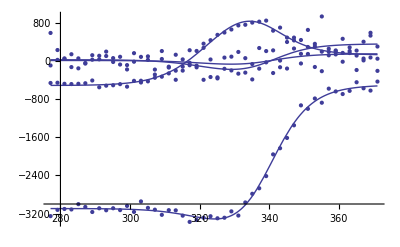

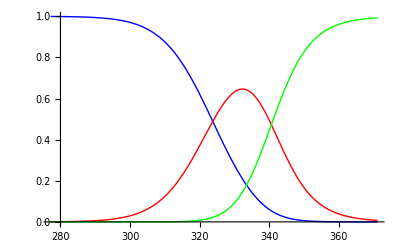

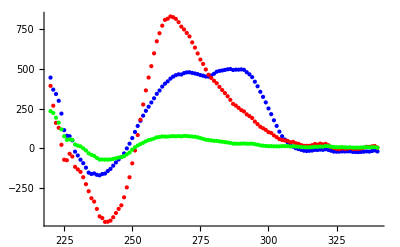

```mathematica
(* Two Transition Fitting *)

(* Two Transition Guesses *)

GuessTable = {};

Sn11Guess = 0;
S11Guess =Sn21Guess= 0;
Su1Guess =  0;

AppendTo[GuessTable, {"Sn11Guess", "S11Guess", "Su1Guess"}];
AppendTo[GuessTable, {Sn11Guess, S11Guess,  Su1Guess}];

Sn12Guess = 0;
S12Guess =Sn22Guess= 0;
Su2Guess = 0;

AppendTo[GuessTable, {"Sn12Guess", "S12Guess", "Su2Guess"}];
AppendTo[GuessTable, {Sn12Guess, S12Guess, Su2Guess}];

Sn13Guess =0;
S13Guess =Sn23Guess= 0;
Su3Guess =  0;

AppendTo[GuessTable, {"Sn13Guess", "S13Guess", "Su3Guess"}];
AppendTo[GuessTable, {Sn13Guess, S13Guess, Su3Guess}];

Sn14Guess =0;
S14Guess =Sn24Guess= 0;
Su4Guess =  0;

AppendTo[GuessTable, {"Sn14Guess", "S14Guess", "Su4Guess"}];
AppendTo[GuessTable, {Sn14Guess, S14Guess, Su4Guess}];

dH1Guess = -30000;
Tm1Guess = GuessHelpTm1+273.15;
dH2Guess = -50000;
Tm2Guess = GuessHelpTm2+273.15;

AppendTo[GuessTable, {"dH1Guess", "Tm1Guess", "dH2Guess", "Tm2Guess"}];
AppendTo[GuessTable, {dH1Guess, Tm1Guess-273.15, dH2Guess,Tm2Guess-273.15}];

R = 1.986;

(* Algorithm *)

Clear[Tm1, Tm2, dH1, dH2]
LinkedChiSquared = Sum[((TwoTransitionModelAll[[i]]/.T->VvectorFullSet[[i,j,1]])-VvectorFullSet[[i,j,2]])^2, {j, Length[VvectorFullSet[[1]]]}, {i, 4}];
BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11,Sn11Guess}, {S11, S11Guess}, {Su1, Su1Guess},{Sn12,Sn12Guess}, {S12, S12Guess},{Su2, Su2Guess},{Sn13, Sn13Guess}, {S13, S13Guess}, {Su3, Su3Guess},{Sn14, Sn14Guess}, {S14, S14Guess}, {Su4, Su4Guess}, {dH1, dH1Guess}, {Tm1, Tm1Guess}, {dH2, dH2Guess}, {Tm2, Tm2Guess}}, Method-> "Automatic", MaxIterations-> 10000];

(* BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11,Sn11Guess}, {S11, S11Guess}, {Su1, Su1Guess},{Sn12,Sn12Guess}, {S12, S12Guess},{Su2, Su2Guess},{Sn13, Sn13Guess}, {S13, S13Guess}, {Su3, Su3Guess}, {dH1, dH1Guess}, {Tm1, Tm1Guess}, {dH2, dH2Guess}, {Tm2, Tm2Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000]; *)

TwoTransitionChiSquared = BestAnswerEver[[1]];
TwoTransitionParameters = 16;
(* TwoTransitionPoints = Sum[Sum[Abs[VvectorFullSet[[q,i,2]]], {i, 1, Length[VvectorFullSet[[q]]]}], {q, 1, 3}]; *)
TwoTransitionPoints =Sum[Length[VvectorFullSet[[i]]], {i, 1, 4}];
TwoTransitionDoF = TwoTransitionPoints - TwoTransitionParameters;
AICTwoTransitions = TwoTransitionPoints*Log[TwoTransitionChiSquared/TwoTransitionPoints]+2*(TwoTransitionParameters+1);

TwoTransitionAnswerTable = {};
AppendTo[TwoTransitionAnswerTable, {"Two Transition Best Fit Results"}];
AppendTo[TwoTransitionAnswerTable, {"Chi Squared", TwoTransitionChiSquared}];
AppendTo[TwoTransitionAnswerTable, {"AIC Value", AICTwoTransitions}];
AppendTo[TwoTransitionAnswerTable, {"  "}];
AppendTo[TwoTransitionAnswerTable, {"Sn11", Sn11/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"S11", S11/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Su1", Su1/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Sn12", Sn12/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"S12", S12/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Su2", Su2/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Sn13", Sn13/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"S13", S13/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Su3", Su3/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Sn14", Sn14/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"S14", S14/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Su4", Su4/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"dH1", dH1*10^-3/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Tm1", Tm1-273.15/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"dH2", dH2*10^-3/.BestAnswerEver[[2]]}];
AppendTo[TwoTransitionAnswerTable, {"Tm2", Tm2-273.15/.BestAnswerEver[[2]]}];
dG1 = (dH1 - (20+273.15)*(dH1/Tm1))/.BestAnswerEver[[2]];
dG2 = (dH2 - (20+273.15)*(dH2/Tm2))/.BestAnswerEver[[2]];
dGTotal = dG1 + dG2;
AppendTo[TwoTransitionAnswerTable, {"dG1", dG1*10^-3}];
AppendTo[TwoTransitionAnswerTable, {"dG2", dG2*10^-3}];
AppendTo[TwoTransitionAnswerTable, {"dGTotal", dGTotal*10^-3}];
AppendTo[TwoTransitionAnswerTable, {" "}];

Print["  "];
Print["Best Guesses"];
Print[TableForm[GuessTable]];
Print["  "];
Print[TableForm[TwoTransitionAnswerTable]];

GlobalPlot1 = Plot[TwoStateMeltingFunction[T,Sn11,S11, Su1, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot2 = Plot[TwoStateMeltingFunction[T,Sn12,S12, Su2, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot3 = Plot[TwoStateMeltingFunction[T,Sn13,S13, Su3, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot4 = Plot[TwoStateMeltingFunction[T,Sn14,S14, Su4, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
TwoTransitionBestFitPlots = Show[GlobalPlot1, GlobalPlot2, GlobalPlot3, GlobalPlot4, P1, P2, P3, P4]

TwoTransitionFits = Table[{Temperatures[[i]]-273.15,VvectorFullSet[[1,i,2]], TwoStateMeltingFunction[Temperatures[[i]],Sn11,S11, Su1, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[1,i,2]]-TwoStateMeltingFunction[Temperatures[[i]],Sn11,S11, Su1, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]],VvectorFullSet[[2,i,2]],TwoStateMeltingFunction[Temperatures[[i]],Sn12,S12, Su2, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[2,i,2]]-TwoStateMeltingFunction[Temperatures[[i]],Sn12,S12, Su2, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[3,i,2]],TwoStateMeltingFunction[Temperatures[[i]],Sn13,S13, Su3, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[3,i,2]]-TwoStateMeltingFunction[Temperatures[[i]],Sn13,S13, Su3, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]]}, {i, 1, Length[Temperatures]}];

TwoTransitionFractionPlots = Show[Plot[TwoStateFractionSn[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Blue],Plot[TwoStateFractionS1[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Red], 
Plot[TwoStateFractionSu[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Green], PlotRange-> All]

TwoTransitionFraction = 
Table[{T-273.15, TwoStateFractionSn[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], TwoStateFractionS1[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], TwoStateFractionSu[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]]}, {T, Temp1, Temp2}];

Species =3;
Newv = Table[Transpose[v][[x]], {x, 1, Species}];
Newv = Transpose[Newv];
News = Table[0, {X, 1, Species}, {Y, 1, Species}];
For[m=1, m≤ Species, m++,
{
News[[m,m]]=s[[m,m]]
}
]
Newu = Table[Transpose[u][[x]], {x, 1, Species}];
Newu = Transpose[Newu];

H1 = ({Sn11/News[[1,1]], Sn12/News[[2,2]], Sn13/News[[3,3]]}/.BestAnswerEver[[2]]);
H2 =({S11/News[[1,1]], S12/News[[2,2]], S13/News[[3,3]]}/.BestAnswerEver[[2]]);
H3= ({Su1/News[[1,1]], Su2/News[[2,2]], Su3/News[[3,3]]}/.BestAnswerEver[[2]]);
Hmatrix = {H1,H2,H3};
DMatrix = Newu.News.Transpose[Hmatrix];

TwoTransitionGeneratedSpectraOutput = Table[Transpose[DMatrix][[i, X]], {X, 1, Length[Wavelengths]}, {i, 1, Species}];
Do[PrependTo[TwoTransitionGeneratedSpectraOutput[[j]], Wavelengths[[j]]], {j, 1, Length[Wavelengths]}];

AllSpecies = {{}, {}, {}};
AllSpecies[[1]] = Table[{Wavelengths[[X]], Transpose[DMatrix][[1, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[2]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[2, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[3]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[3, X]]}, {X, 1, Length[Wavelengths]}];
TwoTransitionSpeciesPlot = ListPlot[AllSpecies, PlotRange-> All, PlotStyle-> {Blue, Red, Green}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Parallel Transition Best Fit Results | 
Chi Squared | 4.70666×10^6
AIC Value | 1974.54
   | 
Sn11 | -3095.51
Sn21 | -3656.84
Su1 | -497.464
Sn12 | -511.053
Sn22 | 1405.34
Su2 | 126.804
Sn13 | 28.3567
Sn23 | -338.406
Su3 | 362.958
Sn14 | 13.4695
Sn24 | -128.389
Su4 | 154.436
dH1 | -68.6367
Tm1 | 60.3425
dH2 | -40.3601
Tm2 | 67.4907
dG1 | -8.30298
dG2 | -5.62683
dGTotal | -13.9298
  |

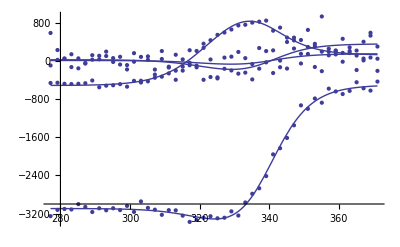

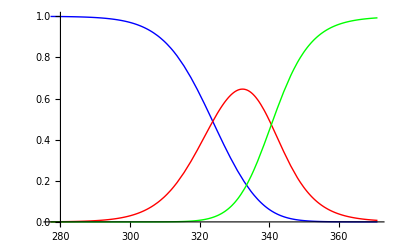

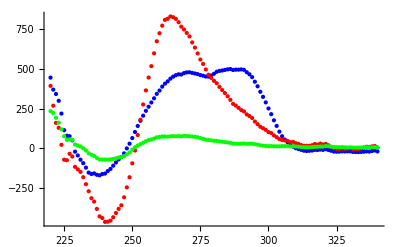

```mathematica
(* Parallel Species Analysis *)

(* Parallel Transition Guesses *)

GuessTable = {};

Sn11Guess = 0;
S11Guess =Sn21Guess= 0;
Su1Guess =  0;

AppendTo[GuessTable, {"Sn11Guess", "Sn21Guess", "Su1Guess"}];
AppendTo[GuessTable, {Sn11Guess, Sn21Guess,  Su1Guess}];

Sn12Guess = 0;
S12Guess =Sn22Guess= 0;
Su2Guess = 0;

AppendTo[GuessTable, {"Sn12Guess", "Sn22Guess", "Su2Guess"}];
AppendTo[GuessTable, {Sn12Guess, Sn22Guess, Su2Guess}];

Sn13Guess =0;
S13Guess =Sn23Guess= 0;
Su3Guess =  0;

AppendTo[GuessTable, {"Sn13Guess", "Sn23Guess", "Su3Guess"}];
AppendTo[GuessTable, {Sn13Guess, Sn23Guess, Su3Guess}];

Sn14Guess =0;
S14Guess =Sn24Guess= 0;
Su4Guess =  0;

AppendTo[GuessTable, {"Sn14Guess", "Sn24Guess", "Su4Guess"}];
AppendTo[GuessTable, {Sn14Guess, Sn24Guess, Su4Guess}];

dH1Guess = -60000;
Tm1Guess = GuessHelpTm2+273.15;
dH2Guess = -40000;
Tm2Guess = GuessHelpTm3+273.15;

AppendTo[GuessTable, {"dH1Guess", "Tm1Guess", "dH2Guess", "Tm2Guess"}];
AppendTo[GuessTable, {dH1Guess, Tm1Guess-273.15, dH2Guess,Tm2Guess-273.15}];

R = 1.986;

(* Algorithm *)

Clear[Tm1, Tm2, dH1, dH2];
LinkedChiSquared = Sum[((ParallelSpeciesModelAll [[i]]/.T->VvectorFullSet[[i,j,1]])-VvectorFullSet[[i,j,2]])^2, {j, Length[VvectorFullSet[[1]]]}, {i, 4}];

BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11,Sn11Guess}, {Sn21, Sn21Guess}, {Su1, Su1Guess},{Sn12,Sn12Guess}, {Sn22, Sn22Guess},{Su2, Su2Guess},{Sn13, Sn13Guess}, {Sn23, Sn23Guess}, {Su3, Su3Guess}, {Sn14, Sn14Guess}, {Sn24, Sn24Guess}, {Su4, Su4Guess},{dH1, dH1Guess}, {Tm1, Tm1Guess}, {dH2, dH2Guess}, {Tm2, Tm2Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000];

(* BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11,Sn11Guess}, {Sn21, Sn21Guess}, {Su1, Su1Guess},{Sn12,Sn12Guess}, {Sn22, Sn22Guess},{Su2, Su2Guess},{Sn13, Sn13Guess}, {Sn23, Sn23Guess}, {Su3, Su3Guess}, {dH1, dH1Guess}, {Tm1, Tm1Guess}, {dH2, dH2Guess}, {Tm2, Tm2Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000]; *)

ParallelTransitionChiSquared = BestAnswerEver[[1]];
ParallelTransitionParameters = 16;
(* ParallelTransitionPoints = Sum[Sum[Abs[VvectorFullSet[[q,i,2]]], {i, 1, Length[VvectorFullSet[[q]]]}], {q, 1, 3}]; *)
ParallelTransitionPoints = Sum[Length[VvectorFullSet[[i]]], {i, 1, 4}];
ParallelTransitionDoF = ParallelTransitionPoints - ParallelTransitionParameters;
AICParallelTransitions = ParallelTransitionPoints*Log[ParallelTransitionChiSquared/ParallelTransitionPoints]+2*(ParallelTransitionParameters+1);

ParallelTransitionAnswerTable = {};
AppendTo[ParallelTransitionAnswerTable, {"Parallel Transition Best Fit Results"}];
AppendTo[ParallelTransitionAnswerTable, {"Chi Squared", ParallelTransitionChiSquared}];
AppendTo[ParallelTransitionAnswerTable, {"AIC Value", AICParallelTransitions}];
AppendTo[ParallelTransitionAnswerTable, {"  "}];
AppendTo[ParallelTransitionAnswerTable, {"Sn11", Sn11/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Sn21", Sn21/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Su1", Su1/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Sn12", Sn12/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Sn22", Sn22/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Su2", Su2/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Sn13", Sn13/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Sn23", Sn23/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Su3", Su3/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Sn14", Sn14/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Sn24", Sn24/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Su4", Su4/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"dH1", dH1*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Tm1", Tm1-273.15/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"dH2", dH2*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ParallelTransitionAnswerTable, {"Tm2", Tm2-273.15/.BestAnswerEver[[2]]}];
dG1 = (dH1 - (20+273.15)*(dH1/Tm1))/.BestAnswerEver[[2]];
dG2 = (dH2 - (20+273.15)*(dH2/Tm2))/.BestAnswerEver[[2]];
dGTotal = dG1 + dG2;
AppendTo[ParallelTransitionAnswerTable, {"dG1", dG1*10^-3}];
AppendTo[ParallelTransitionAnswerTable, {"dG2", dG2*10^-3}];
AppendTo[ParallelTransitionAnswerTable, {"dGTotal", dGTotal*10^-3}];
AppendTo[ParallelTransitionAnswerTable, {" "}];

(* Print["  "];
Print["Best Guesses"];
Print[TableForm[GuessTable]];
Print["  "]; *)
Print[TableForm[ParallelTransitionAnswerTable]];

GlobalPlot1 = Plot[ParallelSpecies[T, Sn11, Sn21, Su1, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot2 = Plot[ParallelSpecies[T, Sn12, Sn22, Su2, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot3 = Plot[ParallelSpecies[T, Sn13, Sn23, Su3, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot4 = Plot[ParallelSpecies[T, Sn14, Sn24, Su4, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
ParallelTransitionBestFitPlots = Show[GlobalPlot1, GlobalPlot2, GlobalPlot3,GlobalPlot4, P1, P2, P3, P4]

ParallelTransitionFits = Table[{Temperatures[[i]]-273.15,VvectorFullSet[[1,i,2]],ParallelSpecies[T = Temperatures[[i]], Sn11, Sn21, Su1, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[1,i,2]]-ParallelSpecies[T = Temperatures[[i]], Sn11, Sn21, Su1, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]],VvectorFullSet[[2,i,2]],ParallelSpecies[T = Temperatures[[i]], Sn12, Sn22, Su2, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[2,i,2]]-ParallelSpecies[T = Temperatures[[i]], Sn12, Sn22, Su2, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[3,i,2]],ParallelSpecies[T = Temperatures[[i]], Sn13, Sn23, Su3, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], VvectorFullSet[[3,i,2]]-ParallelSpecies[T = Temperatures[[i]], Sn13, Sn23, Su3, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]]}, {i, 1, Length[Temperatures]}];
Clear[T];

ParallelTransitionFractionPlots = Show[Plot[ParallelFractionSn1[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Blue],Plot[ParallelFractionSn2[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Red], 
Plot[ParallelFractionSu[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Green], PlotRange-> All]

ParallelTransitionFraction = 
Table[{T-273.15, ParallelFractionSn1[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], ParallelFractionSn2[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]], ParallelFractionSu[T, dH1, Tm1, dH2, Tm2]/.BestAnswerEver[[2]]}, {T, Temp1, Temp2}];

Species =3;

Newv = Table[Transpose[v][[x]], {x, 1, Species}];
Newv = Transpose[Newv];
News = Table[0, {X, 1, Species}, {Y, 1, Species}];
For[m=1, m≤ Species, m++,
{
News[[m,m]]=s[[m,m]]
}
]
Newu = Table[Transpose[u][[x]], {x, 1, Species}];
Newu = Transpose[Newu];

H1 = ({Sn11/News[[1,1]], Sn12/News[[2,2]], Sn13/News[[3,3]]}/.BestAnswerEver[[2]]);
H2 =({Sn21/News[[1,1]], Sn22/News[[2,2]], Sn23/News[[3,3]]}/.BestAnswerEver[[2]]);
H3= ({Su1/News[[1,1]], Su2/News[[2,2]], Su3/News[[3,3]]}/.BestAnswerEver[[2]]);
Hmatrix = {H1,H2,H3};
DMatrix = Newu.News.Transpose[Hmatrix];

ParallelTransitionGeneratedSpectraOutput = Table[Transpose[DMatrix][[i, X]], {X, 1, Length[Wavelengths]}, {i, 1, Species}];
Do[PrependTo[ParallelTransitionGeneratedSpectraOutput[[j]], Wavelengths[[j]]], {j, 1, Length[Wavelengths]}];

AllSpecies = {{}, {}, {}};
AllSpecies[[1]] = Table[{Wavelengths[[X]], Transpose[DMatrix][[1, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[2]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[2, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[3]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[3, X]]}, {X, 1, Length[Wavelengths]}];
ParallelTransitionSpeciesPlot = ListPlot[AllSpecies, PlotRange-> All, PlotStyle-> {Blue, Red, Green}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

Best Guesses

Sn11Guess | S11Guess | S21Guess | Su1Guess |  | 
0 | 0 | 0 | 0 |  | 
Sn12Guess | S12Guess | S22Guess | Su2Guess |  | 
0 | 0 | 0 | 0 |  | 
Sn13Guess | S13Guess | S23Guess | Su3Guess |  | 
0 | 0 | 0 | 0 |  | 
Sn14Guess | S14Guess | S24Guess | Su4Guess |  | 
0 | 0 | 0 | 0 |  | 
dH1Guess | Tm1Guess | dH2Guess | Tm2Guess | dH3Guess | Tm3Guess
-20000 | 28.45 | -40000 | 63.49 | -60000 | 87.85

Three Transition Best Fit Results | 
Chi Squared | 4.27226×10^6
AIC Value | 1967.95
   | 
Sn11 | -3096.15
S11 | -3618.97
S21 | -506.805
Su1 | -529.634
Sn12 | -506.529
S12 | 1231.49
S22 | 230.557
Su2 | -1.75209
Sn13 | 42.0744
S13 | -424.302
S23 | 592.074
Su3 | -47.9589
Sn14 | 5.44912
S14 | -53.3915
S24 | 16.4445
Su4 | 386.093
dH1 | -30.4822
Tm1 | 49.1776
dH2 | -39.6303
Tm2 | 67.8527
dH3 | -47.8721
Tm3 | 90.9876
dG1 | -2.7593
dG2 | -5.5613
dG3 | -9.33253
dGTotal | -17.6531
  |

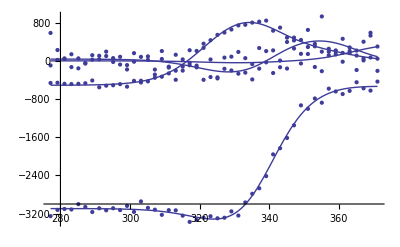

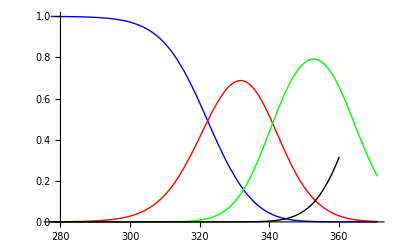

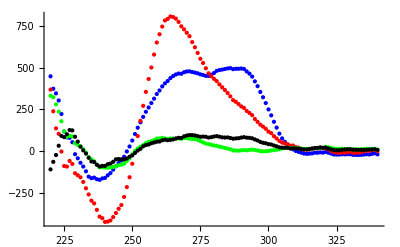

```mathematica
(* Three Transition Model *)

(* Three Transition Guesses *)

GuessTable = {};

Sn11Guess = 0;
S11Guess =Sn21Guess= 0;
S21Guess = 0;
Su1Guess =  0;

AppendTo[GuessTable, {"Sn11Guess", "S11Guess","S21Guess", "Su1Guess"}];
AppendTo[GuessTable, {Sn11Guess, S11Guess,S21Guess,  Su1Guess}];

Sn12Guess = 0;
S12Guess =Sn22Guess= 0;
S22Guess = 0;
Su2Guess =  0;

AppendTo[GuessTable, {"Sn12Guess", "S12Guess","S22Guess", "Su2Guess"}];
AppendTo[GuessTable, {Sn12Guess, S12Guess,S22Guess,  Su2Guess}];

Sn13Guess =0;
S13Guess =Sn23Guess= 0;
S23Guess = 0;
Su3Guess = 0;

AppendTo[GuessTable, {"Sn13Guess", "S13Guess","S23Guess", "Su3Guess"}];
AppendTo[GuessTable, {Sn13Guess, S13Guess,S23Guess,  Su3Guess}];

Sn14Guess = 0;
S14Guess =Sn24Guess= 0;
S24Guess = 0;
Su4Guess =  0;

AppendTo[GuessTable, {"Sn14Guess", "S14Guess","S24Guess", "Su4Guess"}];
AppendTo[GuessTable, {Sn14Guess, S14Guess,S24Guess,  Su4Guess}];

dH1Guess = -20000;
Tm1Guess = GuessHelpTm1+273.15;
dH2Guess = -40000;
Tm2Guess =GuessHelpTm2+273.15;
dH3Guess = -60000;
Tm3Guess = GuessHelpTm3+273.15;

AppendTo[GuessTable, {"dH1Guess", "Tm1Guess","dH2Guess", "Tm2Guess", "dH3Guess", "Tm3Guess"}];
AppendTo[GuessTable, {dH1Guess, Tm1Guess-273.15,dH2Guess,  Tm2Guess-273.15,dH3Guess,Tm3Guess-273.15 }];

R = 1.986;

(* Algorithm *)

LinkedChiSquared = Sum[((ThreeTransitionModelAll[[i]]/.T->VvectorFullSet[[i,j,1]])-VvectorFullSet[[i,j,2]])^2, {j, Length[VvectorFullSet[[1]]]}, {i, 4}];

BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11, Sn11Guess}, {S11, S11Guess},{S21, S21Guess}, {Su1, Su1Guess},{Sn12,Sn12Guess}, {S12,S12Guess},{S22, S22Guess}, {Su2, Su2Guess},{Sn13,Sn13Guess}, {S13, S13Guess},{S23, S23Guess}, {Su3, Su3Guess}, {Sn14,Sn14Guess}, {S14, S14Guess},{S24, S24Guess}, {Su4, Su4Guess},{dH1, dH1Guess}, {Tm1, Tm1Guess}, {dH2, dH2Guess}, {Tm2, Tm2Guess}, {dH3, dH3Guess}, {Tm3,Tm3Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000];
 (* BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11, Sn11Guess}, {S11, S11Guess},{S21, S21Guess}, {Su1, Su1Guess},{Sn12,Sn12Guess}, {S12,S12Guess},{S22, S22Guess}, {Su2, Su2Guess},{Sn13,Sn13Guess}, {S13, S13Guess},{S23, S23Guess}, {Su3, Su3Guess}, {Sn14,Sn14Guess}, {S14, S14Guess},{S24, S24Guess}, {Su4, Su4Guess},{dH1, dH1Guess}, {Tm1, Tm1Guess}, {dH2, dH2Guess}, {Tm2, Tm2Guess}, {dH3, dH3Guess}, {Tm3,Tm3Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000]; *)

ThreeTransitionChiSquared = BestAnswerEver[[1]];
ThreeTransitionParameters = 22;
(* ThreeTransitionPoints = Sum[Sum[Abs[VvectorFullSet[[q,i,2]]], {i, 1, Length[VvectorFullSet[[q]]]}], {q, 1, 4}]; *)
ThreeTransitionPoints = Sum[Length[VvectorFullSet[[i]]], {i, 1, 4}];
ThreeTransitionDoF = ThreeTransitionPoints - ThreeTransitionParameters;
AICThreeTransitions = ThreeTransitionPoints*Log[ThreeTransitionChiSquared/ThreeTransitionPoints]+2*(ThreeTransitionParameters+1);

ThreeTransitionAnswerTable = {};
AppendTo[ThreeTransitionAnswerTable, {"Three Transition Best Fit Results"}];
AppendTo[ThreeTransitionAnswerTable, {"Chi Squared", ThreeTransitionChiSquared}];
AppendTo[ThreeTransitionAnswerTable, {"AIC Value", AICThreeTransitions}];
AppendTo[ThreeTransitionAnswerTable, {"  "}];
AppendTo[ThreeTransitionAnswerTable, {"Sn11", Sn11/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S11", S11/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S21", S21/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Su1", Su1/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Sn12", Sn12/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S12", S12/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S22", S22/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Su2", Su2/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Sn13", Sn13/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S13", S13/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S23", S23/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Su3", Su3/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Sn14", Sn14/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S14", S14/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"S24", S24/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Su4", Su4/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"dH1", dH1*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Tm1", Tm1-273.15/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"dH2", dH2*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Tm2", Tm2-273.15/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"dH3", dH3*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ThreeTransitionAnswerTable, {"Tm3", Tm3-273.15/.BestAnswerEver[[2]]}];
dG1 = (dH1 - (20+273.15)*(dH1/Tm1))/.BestAnswerEver[[2]];
dG2 = (dH2 - (20+273.15)*(dH2/Tm2))/.BestAnswerEver[[2]];
dG3 = (dH3 - (20+273.15)*(dH3/Tm3))/.BestAnswerEver[[2]];
dGTotal = dG1 + dG2 + dG3;
AppendTo[ThreeTransitionAnswerTable, {"dG1", dG1*10^-3}];
AppendTo[ThreeTransitionAnswerTable, {"dG2", dG2*10^-3}];
AppendTo[ThreeTransitionAnswerTable, {"dG3", dG3*10^-3}];
AppendTo[ThreeTransitionAnswerTable, {"dGTotal", dGTotal*10^-3}];
AppendTo[ThreeTransitionAnswerTable, {" "}];

Print["  "];
Print["Best Guesses"];
Print[TableForm[GuessTable]];
Print["  "];
Print[TableForm[ThreeTransitionAnswerTable]];

GlobalPlot1 = Plot[ThreeStateMeltingFunction[T,Sn11,S11, S21, Su1, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot2 = Plot[ThreeStateMeltingFunction[T,Sn12,S12, S22, Su2, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot3 = Plot[ThreeStateMeltingFunction[T,Sn13,S13, S23, Su3, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot4 = Plot[ThreeStateMeltingFunction[T,Sn14,S14, S24, Su4, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
ThreeTransitionBestFitPlots = Show[GlobalPlot1, GlobalPlot2, GlobalPlot3, GlobalPlot4, P1, P2, P3, P4, PlotRange-> All]

ThreeTransitionFits = Table[{Temperatures[[i]]-273.15,VvectorFullSet[[1,i,2]],ThreeStateMeltingFunction[T=Temperatures[[i]],Sn11,S11, S21, Su1, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[1,i,2]]-ThreeStateMeltingFunction[T=Temperatures[[i]],Sn11,S11, S21, Su1, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]],VvectorFullSet[[2,i,2]], ThreeStateMeltingFunction[T=Temperatures[[i]],Sn12,S12, S22, Su2, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[2,i,2]]- ThreeStateMeltingFunction[T=Temperatures[[i]],Sn12,S12, S22, Su2, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]],VvectorFullSet[[3,i,2]], ThreeStateMeltingFunction[T = Temperatures[[i]],Sn13,S13, S23, Su3, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[3,i,2]]-ThreeStateMeltingFunction[T = Temperatures[[i]],Sn13,S13, S23, Su3, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[4,i,2]], ThreeStateMeltingFunction[T = Temperatures[[i]],Sn14,S14, S24, Su4, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[4,i,2]]-ThreeStateMeltingFunction[T = Temperatures[[i]],Sn14,S14, S24, Su4, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]]}, {i, 1, Length[Temperatures]}];
Clear[T];

ThreeTransitionFractionPlots = Show[Plot[ThreeStateFractionSn[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Blue],Plot[ThreeStateFractionS1[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Red],
Plot[ThreeStateFractionS2[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Green],
Plot[ThreeStateFractionSu[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Black], PlotRange-> All]

ThreeTransitionFraction = 
Table[{T-273.15, ThreeStateFractionSn[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], ThreeStateFractionS1[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]],ThreeStateFractionS2[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], ThreeStateFractionSu[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]]}, {T, Temp1, Temp2}];

Species =4;

Newv = Table[Transpose[v][[x]], {x, 1, Species}];
Newv = Transpose[Newv];
MatrixForm[Newv];
ListPlot[Transpose[Newv][[3]]];

News = Table[0, {X, 1, Species}, {Y, 1, Species}];
For[m=1, m≤ Species, m++,
{
News[[m,m]]=s[[m,m]]
}
]
MatrixForm[News];

Newu = Table[Transpose[u][[x]], {x, 1, Species}];
Newu = Transpose[Newu];
MatrixForm[Newu];

MatrixForm[Newu.News.Transpose[Newv]];

H1 = ({Sn11/News[[1,1]], Sn12/News[[2,2]], Sn13/News[[3,3]], Sn14/News[[4,4]]}/.BestAnswerEver[[2]]);
H2 =({S11/News[[1,1]], S12/News[[2,2]], S13/News[[3,3]], S14/News[[4,4]]}/.BestAnswerEver[[2]]);
H3 =({S21/News[[1,1]], S22/News[[2,2]], S23/News[[3,3]], S24/News[[4,4]]}/.BestAnswerEver[[2]]);
H4 = ({Su1/News[[1,1]], Su2/News[[2,2]], Su3/News[[3,3]], Su4/News[[4,4]]}/.BestAnswerEver[[2]]);
Hmatrix = {H1,H2,H3, H4};
DMatrix = Newu.News.Transpose[Hmatrix];

ThreeTransitionGeneratedSpectraOutput = Table[Transpose[DMatrix][[i, X]], {X, 1, Length[Wavelengths]}, {i, 1, Species}];
Do[PrependTo[ThreeTransitionGeneratedSpectraOutput[[j]], Wavelengths[[j]]], {j, 1, Length[Wavelengths]}];

AllSpecies = {{}, {}, {}, {}};
AllSpecies[[1]] = Table[{Wavelengths[[X]], Transpose[DMatrix][[1, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[2]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[2, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[3]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[3, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[4]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[4, X]]}, {X, 1, Length[Wavelengths]}];
ThreeTransitionSpeciesPlot = ListPlot[AllSpecies, PlotStyle-> {Blue,Red,Green,Black},PlotRange-> All]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Best Guesses

Sn11Guess | S11Guess | S21Guess | Su1Guess |  | 
0 | 0 | 0 | 0 |  | 
Sn12Guess | S12Guess | S22Guess | Su2Guess |  | 
0 | 0 | 0 | 0 |  | 
Sn13Guess | S13Guess | S23Guess | Su3Guess |  | 
0 | 0 | 0 | 0 |  | 
Sn14Guess | S14Guess | S24Guess | Su4Guess |  | 
0 | 0 | 0 | 0 |  | 
dH1Guess | Tm1Guess | dH2Guess | Tm2Guess | dH3Guess | Tm3Guess
-60000 | 28.45 | -30000 | 63.49 | -40000 | 87.85

Parallel Intermediate Transition Best Fit Results | 
Chi Squared | 4.70666×10^6
AIC Value | 1986.54
   | 
Sn11 | -147.662
Sn21 | -3095.5
S21 | -3656.91
Su1 | -497.47
Sn12 | -142.409
Sn22 | -511.07
S22 | 1405.53
Su2 | 126.794
Sn13 | 134.916
Sn23 | 28.36
S23 | -338.445
Su3 | 362.959
Sn14 | -5.73713
Sn24 | 13.4713
S24 | -128.405
Su4 | 154.436
dH1 | -59.9951
Tm1 | -33.3529
dH2 | -28.2721
Tm2 | 50.6461
dH3 | -40.3596
Tm3 | 67.4902
dG1 | 13.3484
dG2 | -2.67585
dG3 | -5.62671
dGTotal | 5.04584
  |

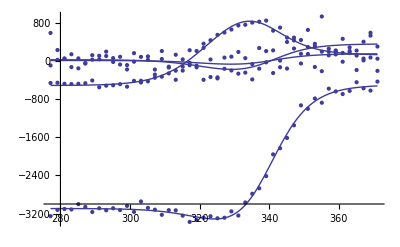

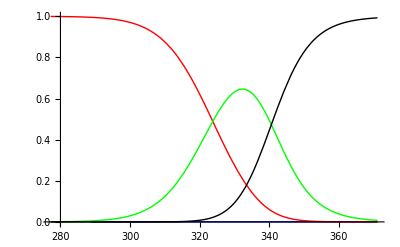

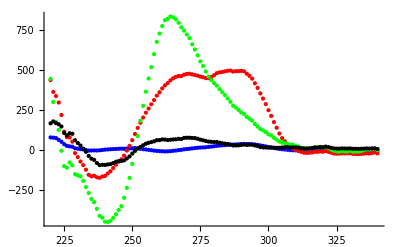

```mathematica
(* Parallel Intermediate Transition Model *)

(* Parallel Intermediate Transition Guesses *)

GuessTable = {};

Sn11Guess = 0;
S11Guess =Sn21Guess= 0;
S21Guess = 0;
Su1Guess =  0;

AppendTo[GuessTable, {"Sn11Guess", "S11Guess","S21Guess", "Su1Guess"}];
AppendTo[GuessTable, {Sn11Guess, S11Guess,S21Guess,  Su1Guess}];

Sn12Guess = 0;
S12Guess =Sn22Guess= 0;
S22Guess = 0;
Su2Guess =  0;

AppendTo[GuessTable, {"Sn12Guess", "S12Guess","S22Guess", "Su2Guess"}];
AppendTo[GuessTable, {Sn12Guess, S12Guess,S22Guess,  Su2Guess}];

Sn13Guess =0;
S13Guess =Sn23Guess= 0;
S23Guess = 0;
Su3Guess = 0;

AppendTo[GuessTable, {"Sn13Guess", "S13Guess","S23Guess", "Su3Guess"}];
AppendTo[GuessTable, {Sn13Guess, S13Guess,S23Guess,  Su3Guess}];

Sn14Guess = 0;
S14Guess =Sn24Guess= 0;
S24Guess = 0;
Su4Guess =  0;

AppendTo[GuessTable, {"Sn14Guess", "S14Guess","S24Guess", "Su4Guess"}];
AppendTo[GuessTable, {Sn14Guess, S14Guess,S24Guess,  Su4Guess}];

dH1Guess = -60000;
Tm1Guess =GuessHelpTm1+273.15;
dH2Guess = -30000;
Tm2Guess = GuessHelpTm2+273.15;
dH3Guess = -40000;
Tm3Guess = GuessHelpTm3+273.15;

AppendTo[GuessTable, {"dH1Guess", "Tm1Guess","dH2Guess", "Tm2Guess", "dH3Guess", "Tm3Guess"}];
AppendTo[GuessTable, {dH1Guess, Tm1Guess-273.15,dH2Guess,  Tm2Guess-273.15,dH3Guess,Tm3Guess-273.15}];

R = 1.986;

(* Algorithm *)

LinkedChiSquared = Sum[((ParallelIntModelAll[[i]]/.T->VvectorFullSet[[i,j,1]])-VvectorFullSet[[i,j,2]])^2,  {i, 4}, {j, Length[VvectorFullSet[[1]]]}];
BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11,Sn11Guess},{Sn21,Sn21Guess},{S21, S21Guess}, {Su1,Su1Guess},{Sn12,Sn12Guess},{Sn22,Sn22Guess},{S22, S22Guess}, {Su2,Su2Guess},{Sn13,Sn13Guess},{Sn23,Sn23Guess},{S23, S23Guess}, {Su3,Su3Guess},{Sn14,Sn14Guess},{Sn24,Sn24Guess},{S24, S24Guess}, {Su4,Su4Guess},{dH1,dH1Guess}, {Tm1,Tm1Guess}, {dH2,dH2Guess}, {Tm2, Tm2Guess}, {dH3, dH3Guess}, {Tm3, Tm3Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000];

(* BestAnswerEver = FindMinimum[{LinkedChiSquared}, {{Sn11,Sn11Guess},{Sn21,Sn21Guess},{S21, S21Guess}, {Su1,Su1Guess},{Sn12,Sn12Guess},{Sn22,Sn22Guess},{S22, S22Guess}, {Su2,Su2Guess},{Sn13,Sn13Guess},{Sn23,Sn23Guess},{S23, S23Guess}, {Su3,Su3Guess},{Sn14,Sn14Guess},{Sn24,Sn24Guess},{S24, S24Guess}, {Su4,Su4Guess},{dH1,dH1Guess}, {Tm1,Tm1Guess}, {dH2,dH2Guess}, {Tm2, Tm2Guess}, {dH3, dH3Guess}, {Tm3, Tm3Guess}}, Method-> "ConjugateGradient", MaxIterations-> 10000]; *)

ParallelIntermediateTransitionChiSquared = BestAnswerEver[[1]];
ParallelIntermediateTransitionParameters = 22;
(* ParallelIntermediateTransitionPoints = Sum[Sum[Abs[VvectorFullSet[[q,i,2]]], {i, 1, Length[VvectorFullSet[[q]]]}], {q, 1, 4}]; *)
ParallelIntermediateTransitionPoints = Sum[Length[VvectorFullSet[[i]]], {i, 1, 4}];
ParallelIntermediateTransitionDoF = ParallelIntermediateTransitionPoints - ParallelIntermediateTransitionParameters;
AICParallelIntermediatesTransitions = ParallelIntermediateTransitionPoints*Log[ParallelIntermediateTransitionChiSquared/ParallelIntermediateTransitionPoints]+2*(ParallelIntermediateTransitionParameters+1);

ParallelIntermediateTransitionAnswerTable = {};
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Parallel Intermediate Transition Best Fit Results"}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Chi Squared", ParallelIntermediateTransitionChiSquared}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"AIC Value", AICParallelIntermediatesTransitions}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"  "}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn11", Sn11/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn21", Sn21/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"S21", S21/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Su1", Su1/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn12", Sn12/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn22", Sn22/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"S22", S22/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Su2", Su2/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn13", Sn13/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn23", Sn23/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"S23", S23/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Su3", Su3/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn14", Sn14/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Sn24", Sn24/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"S24", S24/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Su4", Su4/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"dH1", dH1*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Tm1", Tm1-273.15/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"dH2", dH2*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Tm2", Tm2-273.15/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"dH3", dH3*10^-3/.BestAnswerEver[[2]]}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"Tm3", Tm3-273.15/.BestAnswerEver[[2]]}];
dG1 = (dH1 - (20+273.15)*(dH1/Tm1))/.BestAnswerEver[[2]];
dG2 = (dH2 - (20+273.15)*(dH2/Tm2))/.BestAnswerEver[[2]];
dG3 = (dH3 - (20+273.15)*(dH3/Tm3))/.BestAnswerEver[[2]];
dGTotal = dG1 + dG2 + dG3;
AppendTo[ParallelIntermediateTransitionAnswerTable, {"dG1", dG1*10^-3}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"dG2", dG2*10^-3}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"dG3", dG3*10^-3}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {"dGTotal", dGTotal*10^-3}];
AppendTo[ParallelIntermediateTransitionAnswerTable, {" "}];

Print["  "];
Print["Best Guesses"];
Print[TableForm[GuessTable]];
Print["  "];
Print[TableForm[ParallelIntermediateTransitionAnswerTable]];

GlobalPlot1 = Plot[ParallelIntermediateFunction[T, Sn11, Sn21, S21, Su1, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot2 = Plot[ParallelIntermediateFunction[T, Sn12, Sn22, S22, Su2, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot3 = Plot[ParallelIntermediateFunction[T, Sn13, Sn23, S23, Su3, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
GlobalPlot4 = Plot[ParallelIntermediateFunction[T, Sn14, Sn24, S24, Su4, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotRange-> All];
ParallelIntermediateTransitionBestFitPlots = Show[GlobalPlot1, GlobalPlot2, GlobalPlot3, GlobalPlot4, P1, P2, P3, P4, PlotRange-> All]

ParallelIntTransitionFits = Table[{Temperatures[[i]]-273.15,VvectorFullSet[[1,i,2]],ParallelIntermediateFunction[T = Temperatures[[i]], Sn11, Sn21, S21, Su1, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[1,i,2]]-ParallelIntermediateFunction[T = Temperatures[[i]], Sn11, Sn21, S21, Su1, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]],VvectorFullSet[[2,i,2]], ParallelIntermediateFunction[T=Temperatures[[i]], Sn12, Sn22, S22, Su2, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[2,i,2]]-ParallelIntermediateFunction[T=Temperatures[[i]], Sn12, Sn22, S22, Su2, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]],VvectorFullSet[[3,i,2]], ParallelIntermediateFunction[T = Temperatures[[i]], Sn13, Sn23, S23, Su3, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[3,i,2]]-ParallelIntermediateFunction[T = Temperatures[[i]], Sn13, Sn23, S23, Su3, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[4,i,2]], ParallelIntermediateFunction[T = Temperatures[[i]], Sn14, Sn24, S24, Su4, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], VvectorFullSet[[4,i,2]]-ParallelIntermediateFunction[T = Temperatures[[i]], Sn14, Sn24, S24, Su4, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]]}, {i, 1, Length[Temperatures]}];
Clear[T];

ParallelIntermediateTransitionFractionPlots = Show[Plot[ParallelIntFractionSn1[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Blue],Plot[ParallelIntFractionSn2[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Red],
Plot[ParallelIntFractionSI[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Green],
Plot[ParallelIntFractionSu[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], {T, Temp1, Temp2}, PlotStyle-> Black], PlotRange-> All]

ParallelIntTransitionFraction = 
Table[{T-273.15, ParallelIntFractionSn1[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]], ParallelIntFractionSn2[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]],ParallelIntFractionSI[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]],ParallelIntFractionSu[T, dH1, Tm1, dH2, Tm2, dH3, Tm3]/.BestAnswerEver[[2]]}, {T, Temp1, Temp2}];

Species =4;

Newv = Table[Transpose[v][[x]], {x, 1, Species}];
Newv = Transpose[Newv];
MatrixForm[Newv];
ListPlot[Transpose[Newv][[3]]];

News = Table[0, {X, 1, Species}, {Y, 1, Species}];
For[m=1, m≤ Species, m++,
{
News[[m,m]]=s[[m,m]]
}
]
MatrixForm[News];

Newu = Table[Transpose[u][[x]], {x, 1, Species}];
Newu = Transpose[Newu];
MatrixForm[Newu];

MatrixForm[Newu.News.Transpose[Newv]];

H1 = ({Sn11/News[[1,1]], Sn12/News[[2,2]], Sn13/News[[3,3]], Sn14/News[[4,4]]}/.BestAnswerEver[[2]]);
H2 =({Sn21/News[[1,1]], Sn22/News[[2,2]], Sn23/News[[3,3]], Sn24/News[[4,4]]}/.BestAnswerEver[[2]]);
H3 =({S21/News[[1,1]], S22/News[[2,2]], S23/News[[3,3]], S24/News[[4,4]]}/.BestAnswerEver[[2]]);
H4 = ({Su1/News[[1,1]], Su2/News[[2,2]], Su3/News[[3,3]], Su4/News[[4,4]]}/.BestAnswerEver[[2]]);
Hmatrix = {H1,H2,H3, H4};
DMatrix = Newu.News.Transpose[Hmatrix];

ParallelIntermediateGeneratedSpectraOutput = Table[Transpose[DMatrix][[i, X]], {X, 1, Length[Wavelengths]}, {i, 1, Species}];
Do[PrependTo[ParallelIntermediateGeneratedSpectraOutput[[j]], Wavelengths[[j]]], {j, 1, Length[Wavelengths]}];

AllSpecies = {{}, {}, {}, {}};
AllSpecies[[1]] = Table[{Wavelengths[[X]], Transpose[DMatrix][[1, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[2]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[2, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[3]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[3, X]]}, {X, 1, Length[Wavelengths]}];
AllSpecies[[4]] =Table[{Wavelengths[[X]], Transpose[DMatrix][[4, X]]}, {X, 1, Length[Wavelengths]}];
ParallelIntermediateTransitionSpeciesPlot = ListPlot[AllSpecies, PlotRange-> All, PlotStyle-> {Blue, Red, Green, Black}]
```

```mathematica
(* AIC *)

(* AICSingleTransition = SingleTransitionPoints*Log[SingleTransitionChiSquared/SingleTransitionPoints]+2*(SingleTransitionParameters+1);
AICTwoTransitions = TwoTransitionPoints*Log[TwoTransitionChiSquared/TwoTransitionPoints]+2*(TwoTransitionParameters+1);
AICParallelTransitions = ParallelTransitionPoints*Log[ParallelTransitionChiSquared/ParallelTransitionPoints]+2*(ParallelTransitionParameters+1);
AICThreeTransitions = ThreeTransitionPoints*Log[ThreeTransitionChiSquared/ThreeTransitionPoints]+2*(ThreeTransitionParameters+1);
AICParallelIntermediatesTransitions = ParallelIntermediateTransitionPoints*Log[ParallelIntermediateTransitionChiSquared/ParallelIntermediateTransitionPoints]+2*(ParallelIntermediateTransitionParameters+1); *)

(* AICSingleTransition = 1*Log[SingleTransitionChiSquared/1]+2*(SingleTransitionParameters+1);
AICTwoTransitions = 2*Log[TwoTransitionChiSquared/2]+2*(TwoTransitionParameters+1);
AICParallelTransitions = 2*Log[ParallelTransitionChiSquared/2]+2*(ParallelTransitionParameters+1);
AICThreeTransitions = 3*Log[ThreeTransitionChiSquared/3]+2*(ThreeTransitionParameters+1);
AICParallelIntermediatesTransitions = 3*Log[ParallelIntermediateTransitionChiSquared/3]+2*(ParallelIntermediateTransitionParameters+1); *)


AICTable = {};
AppendTo[AICTable, {"  ", "Chi Squared", "AIC Value"}];
AppendTo[AICTable, {"Single Transition", SingleTransitionChiSquared, AICSingleTransition}];
AppendTo[AICTable, {"Two Transitions", TwoTransitionChiSquared, AICTwoTransitions}];
AppendTo[AICTable, {"Parallel Transitions",  ParallelTransitionChiSquared,AICParallelTransitions}];
AppendTo[AICTable, {"Three Transitions",  ThreeTransitionChiSquared,AICThreeTransitions}];
AppendTo[AICTable, {"Parallel Interemediate Transitions",  ParallelIntermediateTransitionChiSquared,AICParallelIntermediatesTransitions}];
AppendTo[AICTable, {" "}];
TableForm[AICTable];

(* Data Comparison and Output *)

Print[TableForm[AICTable]]
Print[TableForm[SingleTransitionAnswerTable]]
Print[SingleTransitionBestFitPlots]
Print[SingleTransitionFractionPlots]
Print[SingleTransitionSpeciesPlot]
Print["  "];
Print[TableForm[TwoTransitionAnswerTable]]
Print[TwoTransitionBestFitPlots]
Print[TwoTransitionFractionPlots]
Print[TwoTransitionSpeciesPlot]
Print["  "]
Print[TableForm[ParallelTransitionAnswerTable]]
Print[ParallelTransitionBestFitPlots]
Print[ParallelTransitionFractionPlots]
Print[ParallelTransitionSpeciesPlot]
Print["  "];
Print[TableForm[ThreeTransitionAnswerTable]]
Print[ThreeTransitionBestFitPlots]
Print[ThreeTransitionFractionPlots]
Print[ThreeTransitionSpeciesPlot]
Print["  "]
Print[TableForm[ParallelIntermediateTransitionAnswerTable]]
Print[ParallelIntermediateTransitionBestFitPlots]
Print[ParallelIntermediateTransitionFractionPlots]
Print[ParallelIntermediateTransitionSpeciesPlot]
```

| Chi Squared | AIC Value
Single Transition | 1.40345×10^7 | 2172.31
Two Transitions | 4.70666×10^6 | 1974.54
Parallel Transitions | 4.70666×10^6 | 1974.54
Three Transitions | 4.27226×10^6 | 1967.95
Parallel Interemediate Transitions | 4.70666×10^6 | 1986.54
  |  |

Single Transition Best Fit Results | 
Chi Squared | 1.40345×10^7
AIC Value | 2172.31
  | 
Sn11 | -3210.5
Su1 | -532.224
Sn12 | -77.7844
Su2 | 382.41
Sn13 | -3210.5
Su3 | -532.224
Sn14 | -77.7844
Su4 | 382.41
dH1 | -43.4692
Tm1 | 69.09
dG1 | -6.23512
  |

-Graphics-

-Graphics-

-Graphics-

Two Transition Best Fit Results | 
Chi Squared | 4.70666×10^6
AIC Value | 1974.54
   | 
Sn11 | -3095.52
S11 | -3656.63
Su1 | -497.495
Sn12 | -511.038
S12 | 1405.02
Su2 | 126.838
Sn13 | 28.3536
S13 | -338.329
Su3 | 362.948
Sn14 | 13.4666
S14 | -128.354
Su4 | 154.432
dH1 | -28.282
Tm1 | 50.6416
dH2 | -40.3652
Tm2 | 67.4918
dG1 | -2.67643
dG2 | -5.62766
dGTotal | -8.30409
  |

-Graphics-

-Graphics-

-Graphics-

Parallel Transition Best Fit Results | 
Chi Squared | 4.70666×10^6
AIC Value | 1974.54
   | 
Sn11 | -3095.51
Sn21 | -3656.84
Su1 | -497.464
Sn12 | -511.053
Sn22 | 1405.34
Su2 | 126.804
Sn13 | 28.3567
Sn23 | -338.406
Su3 | 362.958
Sn14 | 13.4695
Sn24 | -128.389
Su4 | 154.436
dH1 | -68.6367
Tm1 | 60.3425
dH2 | -40.3601
Tm2 | 67.4907
dG1 | -8.30298
dG2 | -5.62683
dGTotal | -13.9298
  |

-Graphics-

-Graphics-

-Graphics-

Three Transition Best Fit Results | 
Chi Squared | 4.27226×10^6
AIC Value | 1967.95
   | 
Sn11 | -3096.15
S11 | -3618.97
S21 | -506.805
Su1 | -529.634
Sn12 | -506.529
S12 | 1231.49
S22 | 230.557
Su2 | -1.75209
Sn13 | 42.0744
S13 | -424.302
S23 | 592.074
Su3 | -47.9589
Sn14 | 5.44912
S14 | -53.3915
S24 | 16.4445
Su4 | 386.093
dH1 | -30.4822
Tm1 | 49.1776
dH2 | -39.6303
Tm2 | 67.8527
dH3 | -47.8721
Tm3 | 90.9876
dG1 | -2.7593
dG2 | -5.5613
dG3 | -9.33253
dGTotal | -17.6531
  |

-Graphics-

-Graphics-

-Graphics-

Parallel Intermediate Transition Best Fit Results | 
Chi Squared | 4.70666×10^6
AIC Value | 1986.54
   | 
Sn11 | -147.662
Sn21 | -3095.5
S21 | -3656.91
Su1 | -497.47
Sn12 | -142.409
Sn22 | -511.07
S22 | 1405.53
Su2 | 126.794
Sn13 | 134.916
Sn23 | 28.36
S23 | -338.445
Su3 | 362.959
Sn14 | -5.73713
Sn24 | 13.4713
S24 | -128.405
Su4 | 154.436
dH1 | -59.9951
Tm1 | -33.3529
dH2 | -28.2721
Tm2 | 50.6461
dH3 | -40.3596
Tm3 | 67.4902
dG1 | 13.3484
dG2 | -2.67585
dG3 | -5.62671
dGTotal | 5.04584
  |

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* Output *)

DirectoryTab = {Directory[], {}};
ExportTab = Join[DirectoryTab,AICTable,SingleTransitionAnswerTable, TwoTransitionAnswerTable, ParallelTransitionAnswerTable, ThreeTransitionAnswerTable, ParallelIntermediateTransitionAnswerTable];
TableForm[%]
Export["All_Fits.txt", ExportTab, "Table"]
```

C:\Users\Robert\Desktop\Multi-mer Melts\Octomer Melt |  | 
 |  | 
   | Chi Squared | AIC Value
Single Transition | 1.40345×10^7 | 2172.31
Two Transitions | 4.70666×10^6 | 1974.54
Parallel Transitions | 4.70666×10^6 | 1974.54
Three Transitions | 4.27226×10^6 | 1967.95
Parallel Interemediate Transitions | 4.70666×10^6 | 1986.54
  |  | 
Single Transition Best Fit Results |  | 
Chi Squared | 1.40345×10^7 | 
AIC Value | 2172.31 | 
  |  | 
Sn11 | -3210.5 | 
Su1 | -532.224 | 
Sn12 | -77.7844 | 
Su2 | 382.41 | 
Sn13 | -3210.5 | 
Su3 | -532.224 | 
Sn14 | -77.7844 | 
Su4 | 382.41 | 
dH1 | -43.4692 | 
Tm1 | 69.09 | 
dG1 | -6.23512 | 
  |  | 
Two Transition Best Fit Results |  | 
Chi Squared | 4.70666×10^6 | 
AIC Value | 1974.54 | 
   |  | 
Sn11 | -3095.52 | 
S11 | -3656.63 | 
Su1 | -497.495 | 
Sn12 | -511.038 | 
S12 | 1405.02 | 
Su2 | 126.838 | 
Sn13 | 28.3536 | 
S13 | -338.329 | 
Su3 | 362.948 | 
Sn14 | 13.4666 | 
S14 | -128.354 | 
Su4 | 154.432 | 
dH1 | -28.282 | 
Tm1 | 50.6416 | 
dH2 | -40.3652 | 
Tm2 | 67.4918 | 
dG1 | -2.67643 | 
dG2 | -5.62766 | 
dGTotal | -8.30409 | 
  |  | 
Parallel Transition Best Fit Results |  | 
Chi Squared | 4.70666×10^6 | 
AIC Value | 1974.54 | 
   |  | 
Sn11 | -3095.51 | 
Sn21 | -3656.84 | 
Su1 | -497.464 | 
Sn12 | -511.053 | 
Sn22 | 1405.34 | 
Su2 | 126.804 | 
Sn13 | 28.3567 | 
Sn23 | -338.406 | 
Su3 | 362.958 | 
Sn14 | 13.4695 | 
Sn24 | -128.389 | 
Su4 | 154.436 | 
dH1 | -68.6367 | 
Tm1 | 60.3425 | 
dH2 | -40.3601 | 
Tm2 | 67.4907 | 
dG1 | -8.30298 | 
dG2 | -5.62683 | 
dGTotal | -13.9298 | 
  |  | 
Three Transition Best Fit Results |  | 
Chi Squared | 4.27226×10^6 | 
AIC Value | 1967.95 | 
   |  | 
Sn11 | -3096.15 | 
S11 | -3618.97 | 
S21 | -506.805 | 
Su1 | -529.634 | 
Sn12 | -506.529 | 
S12 | 1231.49 | 
S22 | 230.557 | 
Su2 | -1.75209 | 
Sn13 | 42.0744 | 
S13 | -424.302 | 
S23 | 592.074 | 
Su3 | -47.9589 | 
Sn14 | 5.44912 | 
S14 | -53.3915 | 
S24 | 16.4445 | 
Su4 | 386.093 | 
dH1 | -30.4822 | 
Tm1 | 49.1776 | 
dH2 | -39.6303 | 
Tm2 | 67.8527 | 
dH3 | -47.8721 | 
Tm3 | 90.9876 | 
dG1 | -2.7593 | 
dG2 | -5.5613 | 
dG3 | -9.33253 | 
dGTotal | -17.6531 | 
  |  | 
Parallel Intermediate Transition Best Fit Results |  | 
Chi Squared | 4.70666×10^6 | 
AIC Value | 1986.54 | 
   |  | 
Sn11 | -147.662 | 
Sn21 | -3095.5 | 
S21 | -3656.91 | 
Su1 | -497.47 | 
Sn12 | -142.409 | 
Sn22 | -511.07 | 
S22 | 1405.53 | 
Su2 | 126.794 | 
Sn13 | 134.916 | 
Sn23 | 28.36 | 
S23 | -338.445 | 
Su3 | 362.959 | 
Sn14 | -5.73713 | 
Sn24 | 13.4713 | 
S24 | -128.405 | 
Su4 | 154.436 | 
dH1 | -59.9951 | 
Tm1 | -33.3529 | 
dH2 | -28.2721 | 
Tm2 | 50.6461 | 
dH3 | -40.3596 | 
Tm3 | 67.4902 | 
dG1 | 13.3484 | 
dG2 | -2.67585 | 
dG3 | -5.62671 | 
dGTotal | 5.04584 | 
  |  |

All_Fits.txt

```mathematica
(* Determine which data sets to export *)
ExportMeSingle = 1;
ExportMeTwo = 1;
ExportMeParallel = 1;
ExportMeThree = 1;
ExportMeParInt = 1;

(* Export Single Transition Information *)
If[ExportMeSingle== 1,
{
Export["Single_Transition_Fits_To_Vectors.txt", SingleTransitionFits, "Table"];
Export["Single_Transition_Fraction_Distribution.txt", SingleTransitionFraction, "Table"];
Export["Single_Transition_Generated_Spectra.txt", SingleTransitionGeneratedSpectraOutput, "Table"];
}
];

(* Export Two Transition Fitting Information *)

If[ExportMeTwo== 1,
{
Export["Two_Transition_Fit_to_Vector.txt", TwoTransitionFits, "Table"];
Export["Two_Transition_Fraction_Distribution.txt", TwoTransitionFraction, "Table"];
Export["Two_Transition_Generated_Spectra.txt", TwoTransitionGeneratedSpectraOutput, "Table"];
}
];

(* Export Parallel Transition Fitting Information *)

If[ExportMeParallel== 1,
{
Export["Parallel_Transition_Fit_to_Vectors.txt", ParallelTransitionFits, "Table"];
Export["Parallel_Transition_Fraction_Distribution.txt", ParallelTransitionFraction, "Table"];
Export["Parallel_Transition_Generated_Spectra.txt", ParallelTransitionGeneratedSpectraOutput, "Table"];
}
];

(* Export Three Transition Fitting Information *)

If[ExportMeThree== 1,
{
Export["Three_Transition_Fit_to_Vectors.txt", ThreeTransitionFits, "Table"];
Export["Three_Transition_Fraction_Distribution.txt", ThreeTransitionFraction, "Table"];
Export["Three_Transition_Generated_Spectra.txt", ThreeTransitionGeneratedSpectraOutput, "Table"];
}
];

(* Export Parallel Interemediate Fitting Information *)
If[ExportMeParInt== 1,
{
Export["Parallel_Intermediate_Transition_Fit_to_Vectors.txt", ParallelIntTransitionFits, "Table"];
Export["Parallel_Intermediate_Transition_Fraction_Distribution.txt", ParallelIntTransitionFraction, "Table"];
Export["Parallel_Intermediate_Transition_Generated_Spectra.txt", ParallelIntermediateGeneratedSpectraOutput, "Table"];
}
];
```

```mathematica
Temperatures-273.15
```

{4.,6.,8.,10.,12.,14.,16.,18.,20.,22.,24.,26.,28.,30.,32.,34.,36.,38.,40.,42.,44.,46.,48.,50.,52.,54.,56.,58.,60.,62.,64.,66.,68.,70.,72.,74.,76.,78.,80.,82.,84.,86.,88.,90.,92.,94.,96.,98.}